# 1D LLS

```mathematica
Cc[N_,k_]:= N!/((k-3)!*(N-k)!)
```

```mathematica
Pd[x_]:= x
```

```mathematica
pd[x_]:=1
```

```mathematica
phi[x2_,xk_,N_,k_] := Cc[N,k] *Pd[x2]*(Pd[xk] - Pd[x2])^(k - 3)*(1 - Pd[xk])^(N - k)*pd[x2]*pd[xk]
```

```mathematica
Refine[∫_0^1 ∫_(2xk/3)^xk phi[x2,xk,N,k]ⅆx2ⅆxk, {Element[N,Integers],Element[k,Integers], N>3, k>=2,N>=k}]
```

(3^(1-k) (-1+2 k) N!)/Gamma[1+N]

```mathematica
pi[k_,N_] :=3^(1-k) (-1+2 k)
```

```mathematica
pi[3,10]
```

5/9

```mathematica
pi[5,15]
```

1/9

```mathematica
pi[6,17]
```

11/243

```mathematica
Ck[N_,k_] := 2(N-k)/((N-1)(N-2))
```

```mathematica
tempPh=∑_(k=2)^N Ck[N,k]*pi[k,N]
```

(3^-N (27-23 3^N+18 N+8 3^N N))/(2 (-2+N) (-1+N))

```mathematica
Ph[N_] := (3^-N (27-23 3^N+18 N+8 3^N N))/(2 (-2+N) (-1+N))
N[Ph[10]]
```

0.395858

```mathematica
f[N_] := N/4
```

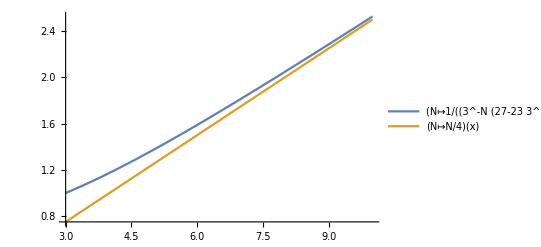

```mathematica
Plot[ {Function[N,1/((3^-N (27-23 3^N+18 N+8 3^N N))/(2 (-2+N) (-1+N)))][x], Function[N,N/4][x]},{x,3,10}, PlotLegends->"Expressions"]
```